```mathematica
(*grades, anonymized, post-first stage processing*)
grades={{4,4,4,4,3,3,4,3,2,3,2,36},{4,4,4,3,0,1,3,3,3,3,1,29},{4,3,4,2,3,1,2,3,0,0,2,24},{4,4,2,2,0,2,2,3,1,2,1,23},{4,4,4,4,1,0,3,0,1,1,2,24},{3,4,4,2,1,1,2,3,0,0,1,21},{4,4,4,4,3,3,2,3,3,3,2,35},{4,4,4,4,3,3,2,3,1,3,2,33},{3,4,4,3,3,3,2,3,0,3,2,30},{4,4,4,3,3,2,2,3,3,0,3,31},{4,3,4,1,3,0,2,1,1,0,0,19},{4,4,4,4,0,0,2,3,3,3,1,28},{4,3,4,3,3,1,4,3,3,3,3,34},{3,0,4,0,3,3,3,0,0,0,2,18},{4,4,4,3,3,0,4,3,3,2,2,32},{3,4,3,3,0,3,3,3,0,3,2,27},{3,3,4,2,3,3,2,3,0,3,2,28},{3,4,1,2,0,3,2,3,1,1,2,22},{3,3,4,2,3,3,2,3,0,2,1,26},{4,3,4,4,2,3,1,2,1,2,2,28},{3,3,4,2,3,3,2,3,1,3,2,29},{2,2,3,0,0,3,2,0,0,0,0,12},{3,2,3,1,1,0,3,0,0,0,1,14},{4,4,4,4,3,3,4,3,3,3,2,37},{4,4,4,2,3,3,2,3,3,3,2,33},{2,1,4,1,0,3,2,2,0,0,0,15},{3,4,4,4,1,0,1,1,0,0,2,20},{4,3,3,2,3,0,2,3,2,3,2,27},{4,3,4,3,2,3,1,3,2,3,2,30},{4,4,4,4,0,3,1,3,1,3,2,29},{3,3,4,3,3,1,2,3,3,3,2,30},{4,4,4,3,3,3,3,3,3,3,2,35},{3,4,4,2,0,3,3,3,2,3,2,29},{3,4,3,3,3,3,3,2,2,3,0,29}};
scores=Transpose[grades];
```

```mathematica
(*compute correlation matrix*)
corr=ConstantArray[0,{Length[scores],Length[scores]}];
For[i=1,i≤Length[scores],i++,
For[j=1,j≤Length[scores],j++,
corr[[i]][[j]]=N[Correlation[scores[[i]],scores[[j]]]];
]
]
```

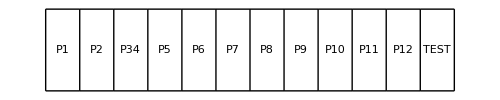
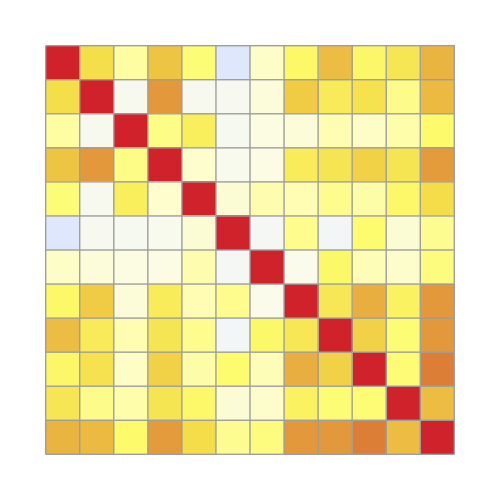
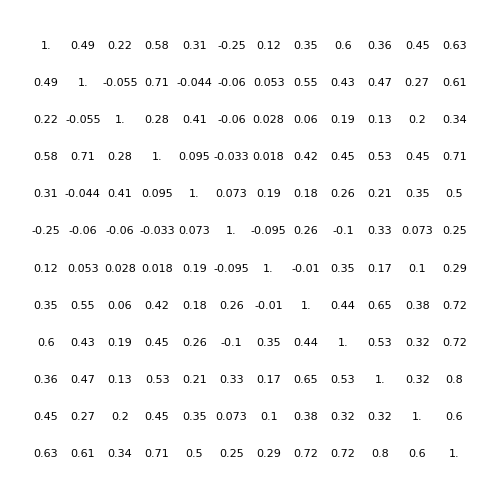
-Graphics-
-Graphics--Graphics--Graphics-

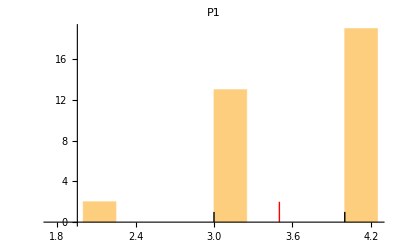
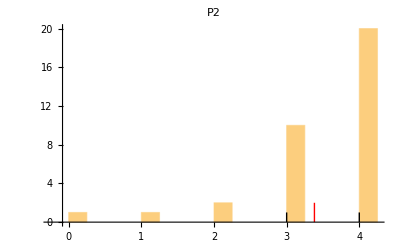
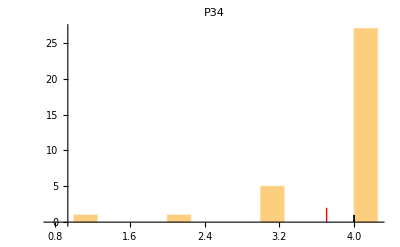
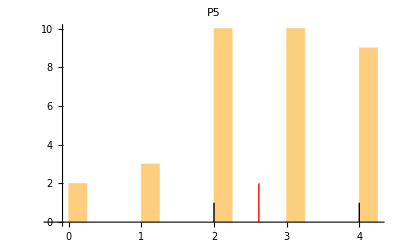
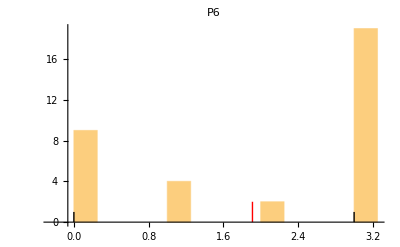
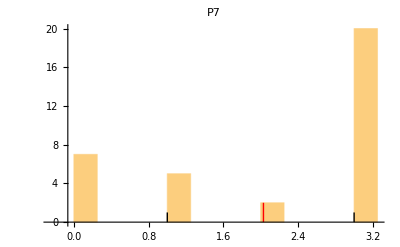
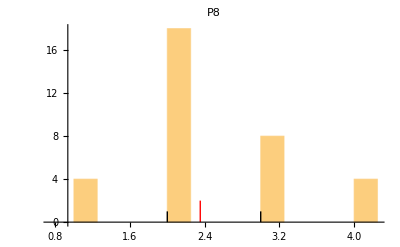
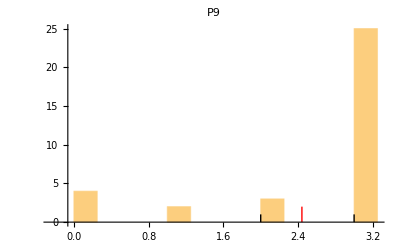

-Graphics-

```mathematica
(*labels for the correlation array*)
labels={P1,P2,P34,P5,P6,P7,P8,P9,P10,P11,P12,TEST};
(*Fancy picture*)
Column[{GraphicsRow[labels,ImageSize->500,Frame->All],Row[{GraphicsColumn[labels,ImageSize->42,Frame->All],Overlay[{ArrayPlot[corr,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,corr,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
(*histograms,for,each,problem,&,test,as,a,whole*)
histograms={};
For[i=1,i≤Length[scores],i++,
histograms=Append[histograms,Histogram[scores[[i]],{.25},Epilog->{Directive[{Thick,Red}],Line[{{Mean[scores[[i]]],0},{Mean[scores[[i]]],2}}],{Directive[{Thick,Black}],Line[{{Quartiles[scores[[i]]][[1]],0},{Quartiles[scores[[i]]][[1]],1}}],Line[{{Quartiles[scores[[i]]][[3]],0},{Quartiles[scores[[i]]][[3]],1}}]}},PlotLabel->labels[[i]]]];
]
histograms
histograms[[Length[histograms]]]
```

```mathematica
Export["test.png",histograms[[10]]]
```

test.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["p1.png"]]]
```